# Power Law

ランク vs. 被引用数等は、zipfの法則に従うとされているが、多くの場合、右肩の下がりが極端になる。
被引用ベクトル空間において、分各野がスパイク状の分布を示すためには右肩の極端な下がりが必要であり、これをモデルに入れない限りスパイク状の分布を再現できない。
これを回避する方法を考えた:
1. zipfの法則の係数を改良する(プロットのshapeが変わらないので本質的改善ではない)
2. モデルの改善(ListLogLogPlot[]のListLogPlot[]が直線になると期待される)

一般的なzipfの法則の式は以下となる （kはランク）:

```mathematica
zipf[k_,s_,n_]:=(1/k^s)/(Sum[1/m,{m,1,n}])
```

係数の決め打ち : 係数を、N = 6000 等に決め打ちして、sのみを算出してみるのはどうか。

それ以外に良く用いられる式は以下である :

```mathematica
zipfc[k_,s_,c_]:=c(1/k^s)
```

上記ではsとcを係数として求める。

```mathematica
zipf[k,s,6000]//N
```

0.107796 k^(-1. s)

```mathematica
zt[1,100]=Table[zipf[k,1,100],{k,1,10}]//N
```

{0.192776,0.0963878,0.0642585,0.0481939,0.0385551,0.0321293,0.0275394,0.024097,0.0214195,0.0192776}

```mathematica
zt[2,100]=Table[zipf[k,2,100],{k,1,10}]//N
```

{0.192776,0.0481939,0.0214195,0.0120485,0.00771103,0.00535488,0.0039342,0.00301212,0.00237995,0.00192776}

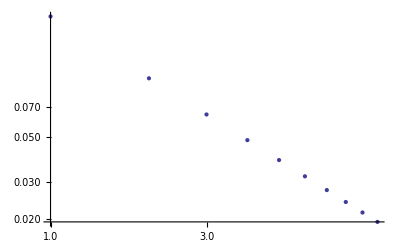

```mathematica
ListLogLogPlot[zt[1,100]]
```

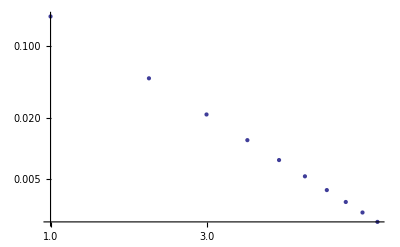

```mathematica
ListLogLogPlot[zt[2,100]]
```